```mathematica
fO= (-O*d+b*Da+2*ep*Da-O^2*a*Di)
fDi= (-Di*gama+ep*Da+th*Dm+(-1/2)*O^2*a*Di)
fDa= (-ep*Da+(1/2)*O^2*a*Di)
fDm= (Di*gama-th*Dm)
con= (1-Di-Da-Dm)
```

b Da+2 Da ep-d O-a Di O^2

Da ep-Di gama-1/2 a Di O^2+Dm th

-Da ep+1/2 a Di O^2

Di gama-Dm th

1-Da-Di-Dm

```mathematica
eq = {fO==0&&fDi==0&&fDa==0&&fDm==0&&con==0}
```

{b Da+2 Da ep-d O-a Di O^2==0&&Da ep-Di gama-1/2 a Di O^2+Dm th==0&&-Da ep+1/2 a Di O^2==0&&Di gama-Dm th==0&&1-Da-Di-Dm==0}

```mathematica
Solve[eq,{O,Di,Da,Dm}]
```

{{O→0,Di→th/(gama+th),Da→0,Dm→gama/(gama+th)},{O→-(-a b th+√a √th √(-8 d^2 ep gama+a b^2 th-8 d^2 ep th))/(2 a d th),Di→(b th+(√th √(-8 d^2 ep gama+a b^2 th-8 d^2 ep th))/(√a))/(2 (b gama+b th)),Da→(b-(√(-8 d^2 ep gama+a b^2 th-8 d^2 ep th))/(√a √th))/(2 b),Dm→(b gama+(gama √(-8 d^2 ep gama+a b^2 th-8 d^2 ep th))/(√a √th))/(2 (b gama+b th))},{O→(a b th+√a √th √(-8 d^2 ep gama+a b^2 th-8 d^2 ep th))/(2 a d th),Di→(b th-(√th √(-8 d^2 ep gama+a b^2 th-8 d^2 ep th))/(√a))/(2 (b gama+b th)),Da→(b+(√(-8 d^2 ep gama+a b^2 th-8 d^2 ep th))/(√a √th))/(2 b),Dm→(b gama-(gama √(-8 d^2 ep gama+a b^2 th-8 d^2 ep th))/(√a √th))/(2 (b gama+b th))}}

```mathematica
{Da,Di,Dm,O}/.%21
```

{{0,th/(gama+th),gama/(gama+th),0},{(b-(√(-8 d^2 ep gama+a b^2 th-8 d^2 ep th))/(√a √th))/(2 b),(b th+(√th √(-8 d^2 ep gama+a b^2 th-8 d^2 ep th))/(√a))/(2 (b gama+b th)),(b gama+(gama √(-8 d^2 ep gama+a b^2 th-8 d^2 ep th))/(√a √th))/(2 (b gama+b th)),-(-a b th+√a √th √(-8 d^2 ep gama+a b^2 th-8 d^2 ep th))/(2 a d th)},{(b+(√(-8 d^2 ep gama+a b^2 th-8 d^2 ep th))/(√a √th))/(2 b),(b th-(√th √(-8 d^2 ep gama+a b^2 th-8 d^2 ep th))/(√a))/(2 (b gama+b th)),(b gama-(gama √(-8 d^2 ep gama+a b^2 th-8 d^2 ep th))/(√a √th))/(2 (b gama+b th)),(a b th+√a √th √(-8 d^2 ep gama+a b^2 th-8 d^2 ep th))/(2 a d th)}}

```mathematica
MatrixForm[%22]
```

(0 | th/(gama+th) | gama/(gama+th) | 0
(b-(√(-8 d^2 ep gama+a b^2 th-8 d^2 ep th))/(√a √th))/(2 b) | (b th+(√th √(-8 d^2 ep gama+a b^2 th-8 d^2 ep th))/(√a))/(2 (b gama+b th)) | (b gama+(gama √(-8 d^2 ep gama+a b^2 th-8 d^2 ep th))/(√a √th))/(2 (b gama+b th)) | -(-a b th+√a √th √(-8 d^2 ep gama+a b^2 th-8 d^2 ep th))/(2 a d th)
(b+(√(-8 d^2 ep gama+a b^2 th-8 d^2 ep th))/(√a √th))/(2 b) | (b th-(√th √(-8 d^2 ep gama+a b^2 th-8 d^2 ep th))/(√a))/(2 (b gama+b th)) | (b gama-(gama √(-8 d^2 ep gama+a b^2 th-8 d^2 ep th))/(√a √th))/(2 (b gama+b th)) | (a b th+√a √th √(-8 d^2 ep gama+a b^2 th-8 d^2 ep th))/(2 a d th))

```mathematica
Manipulate[Plot[Sin[x(1+a x)],{x,0,6}],{a,0,2}]
```

```mathematica
{a, ep, b, th, d} = {1,0.2,1.,0.25,0.22}
```

{1,0.2,1.,0.25,0.22}

```mathematica
(b-(√(-8 d^2 ep gama+a b^2 th-8 d^2 ep th))/(√a √th))/(2 b)
```

0.5 (1.-2. √(0.23064-0.07744 gama))

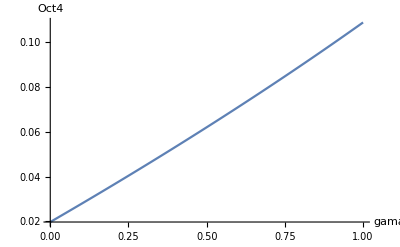

```mathematica
Show[Plot[(b-(√(-8 d^2 ep gama+a b^2 th-8 d^2 ep th))/(√a √th))/(2 b),{gama,0,1}],AxesLabel->{HoldForm[gama],HoldForm[Oct4]},PlotLabel->None,LabelStyle->{GrayLevel[0]}]
```

## 3 D system

```mathematica
fO= (-O*d+b*Da+2*ep*Da-O^2*a*Di)
fDi= (-Di*gama+ep*Da+th*Dm+(-1/2)*O^2*a*Di)
fDa= (-ep*Da+(1/2)*O^2*a*Di)
fDm= (Di*gama-th*Dm)
Da= (1-Di-Dm)
```

b Da+2 Da ep-d O-a Di O^2

Da ep-Di gama-1/2 a Di O^2+Dm th

-Da ep+1/2 a Di O^2

Di gama-Dm th

1-Di-Dm

```mathematica
eq = {fO==0&&fDi==0&&fDm==0&&Da== (1-Di-Dm)}
```

{b (1-Di-Dm)+2 (1-Di-Dm) ep-d O-a Di O^2==0&&(1-Di-Dm) ep-Di gama-1/2 a Di O^2+Dm th==0&&Di gama-Dm th==0}

```mathematica
Solve[eq,{O,Di,Dm}]
```

{{O→0,Di→th/(gama+th),Dm→gama/(gama+th)},{O→(2 b th-(a b^3 gama th)/(a b^2 gama+a b^2 th)-(a b^3 th^2)/(a b^2 gama+a b^2 th)+(√a b^2 gama √th √(-8 d^2 ep gama+a b^2 th-8 d^2 ep th))/(a b^2 gama+a b^2 th)+(√a b^2 th^(3/2) √(-8 d^2 ep gama+a b^2 th-8 d^2 ep th))/(a b^2 gama+a b^2 th))/(2 d th),Di→(a b^2 th-√a b √th √(-8 d^2 ep gama+a b^2 th-8 d^2 ep th))/(2 (a b^2 gama+a b^2 th)),Dm→((a b^2 gama th)/(a b^2 gama+a b^2 th)-(√a b gama √th √(-8 d^2 ep gama+a b^2 th-8 d^2 ep th))/(a b^2 gama+a b^2 th))/(2 th)},{O→(2 b th-(a b^3 gama th)/(a b^2 gama+a b^2 th)-(a b^3 th^2)/(a b^2 gama+a b^2 th)-(√a b^2 gama √th √(-8 d^2 ep gama+a b^2 th-8 d^2 ep th))/(a b^2 gama+a b^2 th)-(√a b^2 th^(3/2) √(-8 d^2 ep gama+a b^2 th-8 d^2 ep th))/(a b^2 gama+a b^2 th))/(2 d th),Di→(a b^2 th+√a b √th √(-8 d^2 ep gama+a b^2 th-8 d^2 ep th))/(2 (a b^2 gama+a b^2 th)),Dm→((a b^2 gama th)/(a b^2 gama+a b^2 th)+(√a b gama √th √(-8 d^2 ep gama+a b^2 th-8 d^2 ep th))/(a b^2 gama+a b^2 th))/(2 th)}}

```mathematica
{Di,Dm,O}/.%44
```

{{th/(gama+th),gama/(gama+th),0},{(a b^2 th-√a b √th √(-8 d^2 ep gama+a b^2 th-8 d^2 ep th))/(2 (a b^2 gama+a b^2 th)),((a b^2 gama th)/(a b^2 gama+a b^2 th)-(√a b gama √th √(-8 d^2 ep gama+a b^2 th-8 d^2 ep th))/(a b^2 gama+a b^2 th))/(2 th),(2 b th-(a b^3 gama th)/(a b^2 gama+a b^2 th)-(a b^3 th^2)/(a b^2 gama+a b^2 th)+(√a b^2 gama √th √(-8 d^2 ep gama+a b^2 th-8 d^2 ep th))/(a b^2 gama+a b^2 th)+(√a b^2 th^(3/2) √(-8 d^2 ep gama+a b^2 th-8 d^2 ep th))/(a b^2 gama+a b^2 th))/(2 d th)},{(a b^2 th+√a b √th √(-8 d^2 ep gama+a b^2 th-8 d^2 ep th))/(2 (a b^2 gama+a b^2 th)),((a b^2 gama th)/(a b^2 gama+a b^2 th)+(√a b gama √th √(-8 d^2 ep gama+a b^2 th-8 d^2 ep th))/(a b^2 gama+a b^2 th))/(2 th),(2 b th-(a b^3 gama th)/(a b^2 gama+a b^2 th)-(a b^3 th^2)/(a b^2 gama+a b^2 th)-(√a b^2 gama √th √(-8 d^2 ep gama+a b^2 th-8 d^2 ep th))/(a b^2 gama+a b^2 th)-(√a b^2 th^(3/2) √(-8 d^2 ep gama+a b^2 th-8 d^2 ep th))/(a b^2 gama+a b^2 th))/(2 d th)}}

```mathematica
MM =MatrixForm[%45]
```

(th/(gama+th) | gama/(gama+th) | 0
(a b^2 th-√a b √th √(-8 d^2 ep gama+a b^2 th-8 d^2 ep th))/(2 (a b^2 gama+a b^2 th)) | ((a b^2 gama th)/(a b^2 gama+a b^2 th)-(√a b gama √th √(-8 d^2 ep gama+a b^2 th-8 d^2 ep th))/(a b^2 gama+a b^2 th))/(2 th) | (2 b th-(a b^3 gama th)/(a b^2 gama+a b^2 th)-(a b^3 th^2)/(a b^2 gama+a b^2 th)+(√a b^2 gama √th √(-8 d^2 ep gama+a b^2 th-8 d^2 ep th))/(a b^2 gama+a b^2 th)+(√a b^2 th^(3/2) √(-8 d^2 ep gama+a b^2 th-8 d^2 ep th))/(a b^2 gama+a b^2 th))/(2 d th)
(a b^2 th+√a b √th √(-8 d^2 ep gama+a b^2 th-8 d^2 ep th))/(2 (a b^2 gama+a b^2 th)) | ((a b^2 gama th)/(a b^2 gama+a b^2 th)+(√a b gama √th √(-8 d^2 ep gama+a b^2 th-8 d^2 ep th))/(a b^2 gama+a b^2 th))/(2 th) | (2 b th-(a b^3 gama th)/(a b^2 gama+a b^2 th)-(a b^3 th^2)/(a b^2 gama+a b^2 th)-(√a b^2 gama √th √(-8 d^2 ep gama+a b^2 th-8 d^2 ep th))/(a b^2 gama+a b^2 th)-(√a b^2 th^(3/2) √(-8 d^2 ep gama+a b^2 th-8 d^2 ep th))/(a b^2 gama+a b^2 th))/(2 d th))

```mathematica
meta = MM[[1,2]]
```

{(0.25-0.5 √(0.23064-0.07744 gama))/(2 (0.25+1. gama)),2. ((0.25 gama)/(0.25+1. gama)-(0.5 √(0.23064-0.07744 gama) gama)/(0.25+1. gama)),9.09091 (0.5-0.0625/(0.25+1. gama)+(0.125 √(0.23064-0.07744 gama))/(0.25+1. gama)-(0.25 gama)/(0.25+1. gama)+(0.5 √(0.23064-0.07744 gama) gama)/(0.25+1. gama))}

```mathematica
{a, ep, b, th, d} = {1,0.2,1.,0.25,0.22}
```

{1,0.2,1.,0.25,0.22}

```mathematica
x = meta[[1]]
y = meta[[2]]
z = meta[[3]]
```

(0.25-0.5 √(0.23064-0.07744 gama))/(2 (0.25+1. gama))

2. ((0.25 gama)/(0.25+1. gama)-(0.5 √(0.23064-0.07744 gama) gama)/(0.25+1. gama))

9.09091 (0.5-0.0625/(0.25+1. gama)+(0.125 √(0.23064-0.07744 gama))/(0.25+1. gama)-(0.25 gama)/(0.25+1. gama)+(0.5 √(0.23064-0.07744 gama) gama)/(0.25+1. gama))